```mathematica
Chaotic Oscillator
```

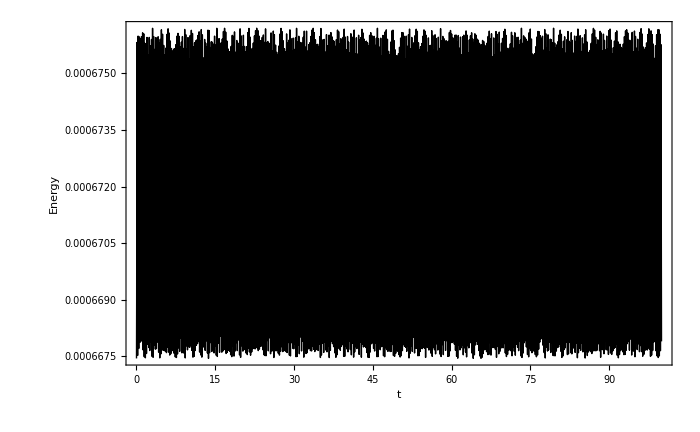

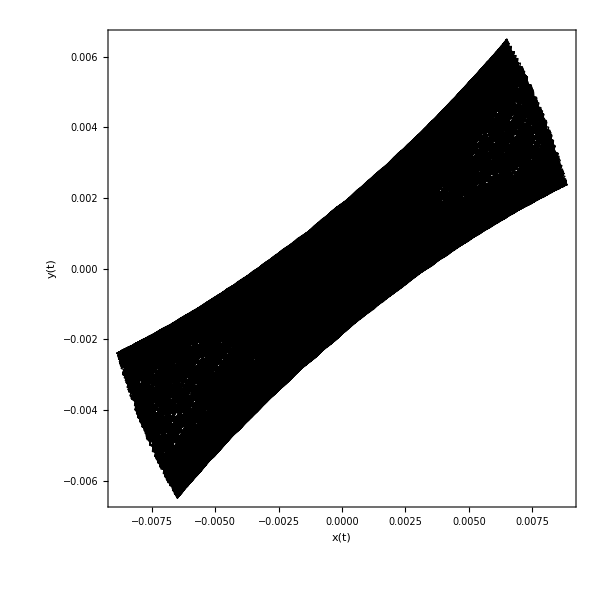

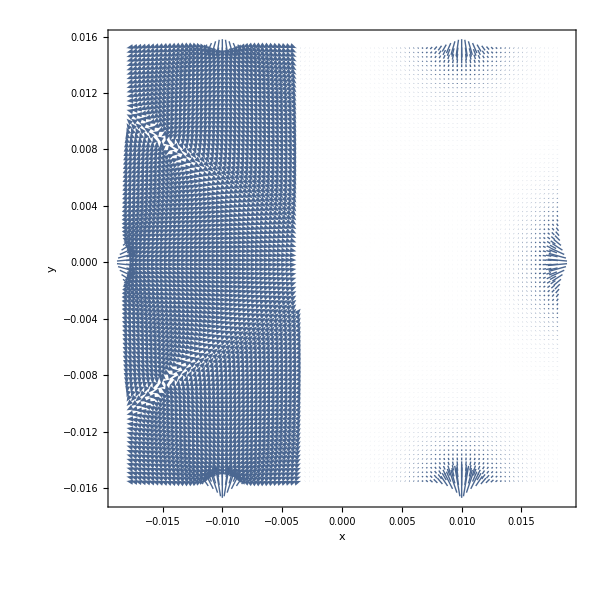

```mathematica
"*****************************************";
" Parameters                             ";
"*****************************************";

"Diameter and height of magnet in m";
height=.005;
diameter=.01;

"Density of magnet in kg/m^3";
ρ=4982;

"Volume of magnet in m^3";
volume=π (diameter/2)^2 height;

"Mass of magnet in kg";
m=volume ρ;

"Permeability of free space in N/A^2";
μ0=4Pi*10^-7;

"Dipole moment in A m^2";
d=.111;

"Gravity in m/s^2";
g={0,0,-9.8};

"Length of the pendulum";
L=.185;

"*****************************************";
" Define force on the particle           ";
"*****************************************";

"Position and velocity vectors. The variables rp and vp refer to the position and velocity vectors for the pendulum magnet, while r1,v1-r6-v6 refer to the 6 magnets found at the vertices of the hexagon.";

k:=1 (* This is just a  parameter to scale up the size of the hexagon*)
rp:={x[t],y[t],.02}
vp:={x'[t],y'[t],0}
r1:=k{.01,.01*√3,0}
v1:={0,0,0}
r2:=k{.02,0,0}
v2:={0,0,0}
r3:=k{.01,-.01*√3,0}
v3:={0,0,0}
r4:=k{-.01,-.01*√3,0}
v4:={0,0,0}
r5:=k{-.02,0,0}
v5:={0,0,0}
r6:=k{-.01,.01*√3,0}
v6:={0,0,0}



"Force vector contribution from one magnet, rp-r is the separation between the pendulum magnet and a 'hexagon magnet,' depending on the choice of r.";

F[r_,v_]:=(3 μ0 d^2)/(2 π)1/((rp-r).(rp-r))^(5/2)(rp-r);


"*****************************************";
" Integrate equations of motion          ";
"*****************************************";
TotalTime=100;

s=NDSolve[{
m x''[t]==F[r1,vp]⟦1⟧+F[r2,vp]⟦1⟧+F[r3,vp]⟦1⟧+F[r4,vp]⟦1⟧+F[r5,vp]⟦1⟧+F[r6,vp]⟦1⟧+m g⟦3⟧rp⟦1⟧/L,
m y''[t]==F[r1,vp]⟦2⟧+F[r2,vp]⟦2⟧+F[r3,vp]⟦2⟧+F[r4,vp]⟦2⟧+F[r5,vp]⟦2⟧+F[r6,vp]⟦2⟧+m g⟦3⟧rp⟦2⟧/L,
m z''[t]==0,
x[0]==.0065,
y[0]==.0065,
z[0]==.02,
x'[0]==0,
y'[0]==0,
z'[0]==0
},{x,y,z},{t,0,TotalTime},MaxSteps->10000000];

"*****************************************";
" Animation                              ";
"*****************************************";
particle[t_]:=Graphics3D[{
Black,Cylinder[{{x[t],y[t],.02-height/2},{x[t],y[t],.02+height/2}},diameter/2]
}]/.s;

penduluml[t_]:=Graphics3D[{
Red,Cylinder[{{x[t],y[t],.02},{0,0,L+z[0]}},diameter/10]
}]/.s;


magnets:=Graphics3D[
{
Black,Cylinder[{{r1⟦1⟧,r1⟦2⟧,-height/2},{r1⟦1⟧,r1⟦2⟧,height/2}},diameter/2],
Black,Cylinder[{{r2⟦1⟧,r2⟦2⟧,-height/2},{r2⟦1⟧,r2⟦2⟧,height/2}},diameter/2],
Black,Cylinder[{{r3⟦1⟧,r3⟦2⟧,-height/2},{r3⟦1⟧,r3⟦2⟧,height/2}},diameter/2],
Black,Cylinder[{{r4⟦1⟧,r4⟦2⟧,-height/2},{r4⟦1⟧,r4⟦2⟧,height/2}},diameter/2],
Black,Cylinder[{{r5⟦1⟧,r5⟦2⟧,-height/2},{r5⟦1⟧,r5⟦2⟧,height/2}},diameter/2],
Black,Cylinder[{{r6⟦1⟧,r6⟦2⟧,-height/2},{r6⟦1⟧,r6⟦2⟧,height/2}},diameter/2]
}]/.s;

Animate[
Show[{
particle[t],
penduluml[t],
magnets
},
PlotRange->{{-.06,.06},{-.06,.06},{-.05,.2}},
ImageSize->300,
Boxed->False,
ViewPoint->Top
],
{t,0,TotalTime},
AnimationRunning->False,
AnimationRate->.43
]



"*****************************************";
" Sanity check: plot the energy          ";
"*****************************************";
Energy[t_]:=(μ0 d^2)/(2π)(1/((rp-r1).(rp-r1))^(3/2)+1/((rp-r2).(rp-r2))^(3/2)+1/((rp-r3).(rp-r3))^(3/2)+1/((rp-r4).(rp-r4))^(3/2)+1/((rp-r5).(rp-r5))^(3/2)+1/((rp-r6).(rp-r6))^(3/2))+((m vp.vp)/2)+1/2((m g[[3]])/L)(x[t]^2+y[t]^2);

Plot[{
(Energy[t]/.s)
},{t,0,TotalTime},
PlotStyle->{Black,Thick},
LabelStyle->25,
ImageSize->700,
PlotRange->All,
Axes->False,
Frame->True,
FrameLabel->{"t","Energy"}
]

"Parametric plot of motion";
ParametricPlot[
Evaluate[{x[t],y[t]}/.s],
{t,0,TotalTime},
AspectRatio->1,
PlotStyle->{Black,Thick},
LabelStyle->25,
ImageSize->600,
PlotRange->All,
Axes->False,
Frame->True,
FrameLabel->{"x(t)","y(t)"}]

"Vector Plot of the force field";
(* For the range, I had to zoom into the interior of the hexagon to get a better view of the force field.  If the actual magnets were in the picture, the force field close to them would blow up and then the scaling would make it very difficult to view anything but a fiew force vectors near the actual positions of the magnets.  I defined a new position vector rg in order to get around the parameterized x[t] and y[t].  Fp is essentially the same as the force vector defined above, but it uses the new position vector rg instead of rp.  This is done just to avoid the parameterized x[t] and y[t] because they are in terms of t so mathematica wouldn't let me define a range of values for x[t] and y[t].  Instead, I just used the new variables v and w.  I still call them x and y in the plot, though, since they mean the same thing. *)
Fp[r_]:=(3 μ0 d^2)/(2 π)1/((rg-r).(rg-r))^(5/2)(rg-r);
rg={v,w,0};
VectorPlot[{Fp[r1][[1]]+Fp[r2][[1]]+Fp[r3][[1]]+Fp[r4][[1]]+Fp[r5][[1]]+Fp[r6][[1]]+m g⟦3⟧rg⟦1⟧/L,Fp[r1][[2]]+Fp[r2][[2]]+Fp[r3][[2]]+Fp[r4][[2]]+Fp[r5][[2]]+Fp[r6][[2]]}+m g⟦3⟧rg⟦2⟧/L,

{v,-.018,.018},
{w,-.0155,.0155},
AspectRatio->1,
LabelStyle->25,
ImageSize->600,
PlotRange->All,
Axes->False,
Frame->True,
FrameLabel->{"x","y"},
VectorPoints->{100,100},
VectorScale->.05]
```